```mathematica
q=26;
TestAlpha[x_]:=0<=x<=q-1
TextCode[messaggio_]:=Select[ToCharacterCode[ToLowerCase[messaggio]]-97,TestAlpha]
FromCode[messaggio_]:=FromCharacterCode[messaggio+97]

EncodingFunction[key_,message_]:=FromCode@Map[ShiftEncrypt[key,#]&,TextCode[message]]
DecodingFunction[key_,message_]:=FromCode@Map[ShiftDecrypt[key,#]&,TextCode[message]]
```

```mathematica
ShiftEncrypt[key_,plaintext_]:=Mod[key+plaintext,q]
ShiftDecrypt[key_,plaintext_]:=ShiftEncrypt[-key,plaintext]
```

```mathematica
DecodingFunction[3,EncodingFunction[3,"ciao a tutti"]]
```

```mathematica
0, ..., 25
```

```mathematica
permutazione={3,2,1,0,5,4,7,6,23,24,25,17,18,11,12,}
```

```mathematica
DEBUG[x___]:=Print[x];
DEBUG[x___]:=Null;


MyPick[stato_]:=Module[{e,lista,perm},
(
lista=stato[[2]];DEBUG[lista];
perm=stato[[1]];DEBUG[perm];
e=RandomInteger[{1,Length[lista]}];DEBUG[e];
{Append[perm,lista[[e]]],Drop[lista,{e}]}
)]
```

```mathematica
lista
```

```mathematica
GenKey[]:=Nest[MyPick,{{},Range[0,q-1]},q][[1]]
```

```mathematica
SubstitutionEncrypt[key_,plaintext_]:=key[[plaintext+1]]
SubstitutionDecrypt[key_,ciphertext_]:=Position[key,ciphertext][[1,1]]-1

EncodingFunction[key_,message_]:=FromCode@Map[SubstitutionEncrypt[key,#]&,TextCode[message]]
DecodingFunction[key_,message_]:=FromCode@Map[SubstitutionDecrypt[key,#]&,TextCode[message]]
```

```mathematica
key=GenKey[]
ctx=EncodingFunction[key,"ciao a tutti"]
DecodingFunction[key,ctx]
```

```mathematica
repubblica=Import["http://www.repubblica.it"];
divina=TextCode[Import["https://www.gutenberg.org/files/1012/1012-0.txt"]];
```

```mathematica
ctx=EncodingFunction[key=GenKey[],repubblica];
```

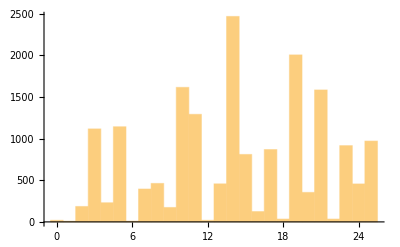

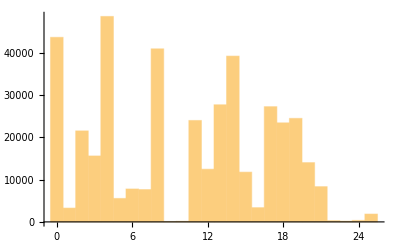

```mathematica
Histogram[TextCode[ctx]]
Histogram[divina]
```

```mathematica
GenKey[]
```

```mathematica
Position[lista,3][[1,1]]
```

```mathematica
ListPlot[key]
```

```mathematica
Position[{1,2,7,3,{1,2,7},{{1,2},{2,3},{3,{7}}}},7]
```

```mathematica
blocksize=6
PermKeyGen[]:=Nest[MyPick,{{},Range[1,blocksize]},blocksize][[1]]

PermutationEncrypt[key_,plaintext_]:=plaintext[[key]]
PermutationDecrypt[key_,ciphertext_]:=Module[{invkey},
invkey=Table[Position[key,i][[1,1]],{i,1,Length@key}];
ciphertext[[invkey]]
]

EncodingFunction[key_,message_]:=FromCode@Flatten@Map[PermutationEncrypt[key,#]&,Partition[TextCode[message],Length[key],Length[key],1,0]]
DecodingFunction[key_,message_]:=FromCode@Flatten@Map[PermutationDecrypt[key,#]&,
Partition[TextCode[message],Length[key],Length[key],1,0]]
```

6

6

{1,6,2,5,4,3}

aabnobtuinemcaeacrbtbanoinaobbadtegiieslimmiedunnaagivzcienoounnettgireploibbaneagitdliimseosizenmimocerncitocnacaualrutdnegisemconoieatsercioigheiergnibeullogtsulaordnmboeademaytuoonsodleiladmiorotpsoacdttpiloipceratrvburiacsehlcusetiseezncrualoelpbbuiuccsaobloraisnnosevrteisapttecposilocrettniogolacvitaaanivogigdeizliinoorcilaolmimaarnaboigbolonearifnnzegeopvanaollapiearpomrrmotaienpsocoiilangcoloiualastoenesgiihcosbeaznarreirepeoruaiilatabrupebdlacieaivaclslniiefraitfiafirndaaznielnevrsdeliporssersonibovnresinznaiusnaictceoighoicsememssegtuadivoiimllliorbamvoroeetnoecgroloiseoroceoroppiulbbcpaohscgoisnliidtizrianoitrecitsewenlreettriezadorncseicveteiomzraargoignlaaotleeralpiulbbczaramooaiggranotalllopeietaciciomonaomdnoiatilaeodizinaicolliirabbnogolanferizoenegvaalimnoopanleilaprrmapomaamortoonirssptropceattollucitluiarvderendvrtpecurisicarniarauissvnaicciflgnoodropmcaastslrugeteuelbneemadobyetuaitlsugoiilatahncetuolmitruaperbabcilionicspleiorcionumceadotltcimoartidoeodizanreeugraarcuisnuraspiliaurnootasisuriestacnaalonvoiizanlelusedcttiilgnaiufcidaeeomitleidenllcfnoistiotctriviinaalletwelstseodrspisreeeclaiseeitnruigidecraarugridaicaulnaodeficvoidniedseirlcitiavlortoeldotlalvnisnienoelilivaegligfdoezriamcsoadbnabomnonaoelmitzlzadinoortsitnaivoacrrodionuzndonocilvidiasjomaceasidrdtulaiaeaznlrlocatiegiduiszitarietnnnaoizaelikeveptersrtepilsiavniiodennhasatagcaranoaconnddiviiorngeusnotioolrpofuuihgcirniaatclociaitinlniosaogmalioovnrejoosnhnanllebaurefdsaonltrrocorniopsdaeetnnltenolroeugroecarnddiviitpeldtoaruddmiolraisplualnimoilteraiatilanfoupnaprideiidllenivdoialraimliuarcndanociividildcopaiostatmoaiggrseuigeapcepvgoardounrceiasmeeriisentnaailieplrencuevorfioisfveisnaarssuianffangnidoicaulnaodeficvoidnitdutitierelseptsopmeocrperdneruegalearlarrauissmleettiatilanlealliesdatiipseaoislitciosasgcnifiaicdnoveilidsdoitreulgalehrcarepcasoudaaccelrlaeairssuateupainneidrrifocacnsechoicinnddiviiasnecraisocfiacalneatalrazivasactledhacepilnusolraeugrnaladocsortoprsirotnnedelgnaiudcomaonlocodiidivsrcaneipcemourfinieelugarurniacarniadiirnecnoarfciehcsndinocisvidiclhadeecridaiodclentftiloemlliaindinsatirovaeitnntnidiennoisengroiiedugireridanfrocirsaecncchinioinviddfifoleerratsgtgaaitoanrooscluntftiloricunabiaanbiotanaoltisduiperbabcilsruamstepnoheeuporrnunanoiauqcsrtepauonnnasruamstepnohenpoccdiidivgleopoiltaciairssuaicbmaaniomldgogelioiunlveomunriolidmqecasuaiatslolnnacvoidnisdelitsoeirpceattoplodioriidleetrotainehclopmirbraellilnedoboohsliilcsaasdopooelrtimleeisiatilanoocajpsositissonocaiccotdoihcinsomiaesvapnntocadiidivrteropeurgniecruarcliaosfertnoirloigntasilaasdlotaorcuiknivotdoudraurdactlolenaabttagildaimailokyleadvnoortsitnaivoacrrodionuzndonociividilipforlsonyleayddarfialooatrgofmaerpiiolupthzcreeahcsatltotaiimgamnleledagfimaleitsartmaniacdnuaoildopmioatroiaprinicdnoviividdseurosniamaiaftsenrtraieistatcnaatnoizbmoecionnolnortargreuardciearnrebineemstnrevegooponrvtitailaladazpiloidanocicvidirciuisrraaniutsaisuvtiitiidvoedmeilobtoacsaodsieluditacirniaaklnatrduossilgnaiufcidaedonocimvidiaorpuilrrotinaoplascsotaoemrapunnertodbnilasturosdonocivvidiiadloebgaattlkiidaiaecivrmrraiasturisiiartpzazalisaevotadllecaatipldenocidvidiuobnilcnaoimifssatoancadnoclleacmsabiuaratsbsodabfiomaaaruqelccasooinviddeibycrtwarathaoccadcrekiyanonmloasuluervtsnsocediidiviirnipcdoipliamtroihoehcacnuoncailosmeaerdiidfeugmlliioomtnedseellpolisondenocikvidiibealvaamnibclaatnancolonoanosrrafidoeznnelebknurunssensoeircaertatrteneeclaleroicemnddiviipiirnriozudotnemeriolopsncunopduongiamcsocrorenicduleaaeihcrdaracoiltteucnrchoinviddtirofeadmierlmezieenykscvcaloinlialvleisriiamadldiinoiceoruoinviddtiniletrsivaimttaaogzzoiilrotnuefesgdgotiackveiolngomigeifelsiiracohvaideisseruerraodlotaitcsirilnapaaozcoznddiviipierloergatilrnipasdavetnaoizeleeuqliamafgnliaifcuuagcaidaslamtroinoladoisortnovtaiftaoiboinccacvoidnimdocibnaetttiigelorntseaanreiianrcuionvialroatnitdutatoomlinidkaoelvreparlebittdamitriosabdinocitvidiercalhuvsaisutoselascracitdniaecrtenoosuvalcderiofmiseaceehcoungeseunpazadvereiigduitstomacdanocievidinaeigrpleortiuorliolledolsasurinaauqtropenoedecudaoveviglerggmiidooisdacreaafflceciricaidroinviddtiideoirlaicnoemmttiideoerlaidoiizempaorueornhcnabtsadaipercaenalliidisgiinnaraittoislsidenniostceonrhaesepseurclmllonioasnecrfiidoecdireosveraedsaleeamrcozaipsavleatnoezlraiiddeembaocreonvitgfllaiidaocneillalboeltrsapicelzeramoimesugsritacgoevnnlilusafvoroeimnimlneapecrheniolsgesiteneviaitinlriepaltasefaadlledloannivnretiaslatmiannainonodaaahgfnmalieizoramoasznedtitiritdaciepraniansiloivpodaaoaucslnaeintoemimsmesamagleotoenpenritttucvoidnisdalitmoairitmasooirsatmibolongogaminoasaraenomttaladaoltnedliedamzonericdetilnaaibctotaleaennavuerensdonocigvidirlebneuaploagtionatiibnicliladaiszevaniocntordnagprateenraiptlaaerbiedirpraaloorsdaaaogcannddiviiovedimgaozritoanrarietnnnaoizarlepeitdiritliledaadnnolraotsiiasidmoobanlsoengiicdnovpididartaircsaeotinsoetoaairpmiodlibtaittoicdnovoimiddaaebeuztapyzgeartefneoioclailoinviddaidombyetuadliiceiebpirrolpmewneemrtifmmenaimelnloosnogdelageeperrzlramoicdnovaisidloudetnlnebelaerfegrifiladgailoelcsenitlgisoteretaicipuvsonaizonelandegienrocediidivseatulleaicsnaztaidpaallaerdetlnlodenpesivieepogrbcelhaemnibnaomannaomaltietamcdanocipvidiriipomavnocoildatiiiabniaanmocrnaelltaaclilcoiedoingateodmierbtliiotltelilnedomnaozruaocivsriometpipamafeargimcidiieclehbcoiccoinviddailimncoimoiiddoiutmreboimmroldepigiaconelhlcraiivzaioonunevaedniguisinlllafaarnaegmoacatnddiviiucsnomzinebivnalaefrsedounqadortueaoeahcnsaecflrnbarutiingoflagiminaepsdreueroaiipnlolnnacvoidnimdoriaesdutnatsseacmireaonivalteatnasaartteerevdeasnuntzetatmorefactuloacmanooicdnovliiidcoamosleeitssaeussllilibcroybsensiatltirebltaroceesrpumranoniiemasnoasaccvoidnigdraieannitlbetcxioldradnouopamneoneczsozonpiertovmalrmtideanrodaaihnuataomelnaimirnieodnnnselizniocodiidivgaevonmriiahotvaniotlivaailtlumsosemadgoigeullalnpnlaarrorafeostatpoeivrlseaznelsauseudigisfeeppiolttecvoidnildbgianrigeaaesilbheattafsnociltiotceodivhoacninottartareduutdnaioonllegeurrerdanocifvidiierzneeoxmdaraeittcactteprrcseieznoinroasnpsrecoseapotrrltsaavgideigageriiomafluiirarilonanvaaluenrgogaicdnoveiridpativvdvaeikirlaidioosidfuipaanitataluctsomleeidssaalecaiimmduilepcshideoofkaicthramyemhsonnkaeonpapizedlnociividilocpmadtitabadgailosnsabcloiemplievaectnireuedactiegidaanculdcioefoinviddpisidaiclicnovtaiduiperbabcilnoeullgboledodmrabaomtneaniiprdnaillvfiotaaobtoincaiccoinviddaiclisposocetrtefomdesabfreraalliosfhactcegcniksduivleloledetlocituerorsbsbaoaottutcvoidnisdomicgarufolnedelialopzsiisacthnaiadaroboncareoiinamfneatsteirrasctitaoinviddiiloptribacuexlleshdgarieirpnsssgniuelualsruenegripeaoifhgucnoepmsnaoizieatutliacidtntidairepmiedsiveenoladoisortnovtaitsoammoaciricdonocilvidiivnretioscatftfareiclapaefsidiennaedcvhnieilaodnedaimriagvoinsnacaaodcoinddiviiammesndueleetsepsrloleciilhcoammavaooprtevrnenoaclinuodanadarrnieucsaisocniulefralaillidaoorznedcecicoicdnoveilidgvalasisnniiiilzneoivalonnpoloiiaopeaflnocinnoceliuarcnmaeidaenleulaairucvoidnildopiiftaciitniveascatatpopaeaelsittntamiaoduficlorepaimggaoarznaaalcelmiederviarelanfgroonnocediidividlnosatgoigrleatiiuasinqruttaorctnooamcsomiatupnrnfnoeenifaliedagiildovaimtnacvoidnitdniietrsivairznegeitsuliemraacguilrmainiabocariosngodoipiplaicitdniameuaeleluorcainddiviicbserigagolihagnuesraaisiootllmpidmiplonaatosoloiriralofttansoocntsiiutcteaerocduliatdiveoicdnovoiridmuasliodcoreiegsuipnpocetiefahnaaizntgorivianraigngocidiidivmiazagnleatiicaetnhtdigiarletereertscshoceaicbmaamdllaacreozorsafaemdisiosnoceinmocidiidivgbrneeliulgeitntesicsonoiobrpoteeociiirtsefuoesrndvilaoiftrelniazztneaidnaasilbaorfnnhccseiicdnovoimiddaaebeuptliyarrentpvaissoearggscsoviosssopinaiomduidivagreolelsritoebnurlslagapienircvoidnigdliiuisvotvvianaaireselomdnodlealltiacucntaruprrooppeismatsoonigeirzzasftidarsaecncsasoroicdnovaisidleusettntamiaimdnoalledegolcuamsarepaelravltasivaeptorgogmaiivlreceildoliardamrniocadiidivcgoisnlaigerllirepaaftseddeallodnianegeiroicnilaoinviddtipervnpoloimaabibciuinrvainieonnogatclociodllazeuhccraoliftdonocirvidiulsaisadmonainpituavtartelriasmfiorcoonsiosiptteidnnofaltusivvioedicrelaoinviddriahkkbibavaottuturntejunsuosaaplladcioufodcedaalleicoicdnovailidrotrpetieattltcsiroasvlatioderlleopoiaptrotnounibrueknearigactcudaoanllesdenocargreuaimdnoanlocediidivcailancaertnlteeletaracissureppiehccsioralnseedleerdotldgiboaoctnemwikalaalrolcvoidniodceincoaimrciuisrcaaniacpasaiectsorumigasethcolaadomrtiepstlibliolcaoclsasuriiavidtatiropdudelaicdnovdieidiatirogceaidcleattotfrefaebmcfdriepaleerpssrsiloiaobbatveounotderiteoderleerpssasohocacttetioreplreottileocilceihgoinviddoitomroiccaredviocnouyhdeausilierttcoordigueaontiozamoindeegeilatdgieidohlgnoidnnocibvidiolriesiisnituveorpamniloilteraeipdreteeplitorilovuosalltlopietsidiaagoillolpmirstsuromfmaialtedagraidsalfeafeircciaorcidnddiviiolrpatceatsasragooilnoieenpetsecrfesrcepoutnesatainamlieramndeeirencodioilcsoogporeelnareeicdnovcisidhaedadllliveloecnisetmsaraaadlgclayihitlimoinirallcataoigedoboecinntgaleioailglciraghsisurinlifaaunsazgclayihptpamaicdnovaigidsactillrianaoisttemoanirdoirteailpalaotfatremhcaproetrlianadmaaacrlildnipneednzraenegaecitdliracoctsatoizrazcvoidnisdelipseotruopbrenpuissuearevpbealrilfimailaeeratprapaomtneidnnocoominiadcaruinaotneoldalnoacitnddiviicidoparsidtelpbbuigcalaitoanraiirgldeozidlyeksndoimisnoalobgcniseoinviddripalismocaaabllefneilliirdlogeairblaemorgcnilooinviddoisaplniuintdripeoddiseeirdoipaoisedlioapoodapildonocilvidiazcerazvanilaesnoidceullreaaniiofttaildedicirlmenrofidacnsecoomlrecvoidnirdaliansgesalaocstaailgurdaoitiiloclmerifeicdnovoifidciurcssaircuiunaparlacunenaieriatilacaoasrlulqcaiisdotigooidleipserrtepiidciloadliafaltameaeptorzcienoimveliornotiaolcserftideecdirealaegniscasoounqeoaensodrlvonoercpmoeisdesiardamrniocadiidivmaylokjsianvcneiergaurreianrcuionnaamnaeileulfelniznoiviilatceonisosnitaeonnotlbemobeodnlasntiorvgiotaioaapmleosivtntocidiidiveingreaslomasaawidsthgniopnrepieeragimlercltisonoepplatorilorduossatlsonrrorocidsnopeanpetoslamotlriloldinocilvidiaodlpimiaaizlreedaisnerpsuisgnpbunitetntendciiffielhcesmirefiedllaneortscsoirrpnoedntiianasrgoniiienotarmtsaoibnoucvoidnimdociuinltitdtoeleusqaseglnalonlidoekwroydoocevnnvovioirssueiuarcniitupncciriancaiceslsapaatidorainnafeanirlnlocidiidivislrepoinggaoedrgasiiaintiuifflomdnoptravioedneiaibtsaalniniaanvousatlledmeallodtpgoatlsonriovniastamosaicomliardnclaemroleepzeltavaeonnitccinamaartseltoepstoalocdmealloctpgooinviddoidlictunemaurtoitatrfonpkpazaniegliroocsrceottheelovvaacalsnaaibcratliadirelinaotnioopidlclanioinviddiireseuaplinotipolniiahtlaacsoesductgtedolniocstrridieltiitpoadarsgsidoonssneecgsilhiedimihngaziodapildonoccvoidnimdoriatconatoaiggodxrofercbmaiidsegsrfediaunsonlrteveeiprrecroadrepgmaiiaegorliezzadeirolnlzadobceogroinviddoitomroiccellabtgaapmirfrearricaiesirldniiierbidbaanueerniltethcablaettersepucdaidraenleiplmlepeignircvoidniednoipsoacdtkccilspvulipuatlionpetoziielaiamreptiidivneiloctmtoraainzzacvoidniededijoahsywmtemiupsacierrrocelreveoicseesdtlieospgniodnoroilgnaiuzcagazoocilnddiviiopnrosetirotiedesainnototcsiriyaeonusroriantocidiidivbsrniattuiffaelpairccalhqluedamaaserliadatfercnaseodofricdnovuiridberhcilmairpabcasoeildalgeairblaemorgfniloeilnilenrilovoececndcatiiiccnotragedeogironaorencohraioecvnonailavlreettarlapeotlsaerlaettadmacaiemhcilreresaaogilrncaihoonmedcarizasotizanuetufrioridcocdralnuuangirodanpmoneerrculapieaneprionorseatitssopaadrfinoccsemleolreiteatlnpesdzoaedilooaiglaiipmdaicalclcaairruosseoptvtroiconsslamecnhireeucrihreghciudsetaiavtnenroanuiassroadcaruiasifogiacidcvoidnildasitloanitsoabekmeattboenirnhscsaiaaiccrieralsaptsodmeaclpoienolciipmovinunipdsoeeotcatloacernddiviibramoausbatsttraeecmisuateaetrcorepealrbernenaiisdapiodliniilcimalaamornnaurboicdnovuiridslsiaicnaotreaamintropidonpagadeaipsgaabiamlbiniargreuarctnooalrcuiuncaargauidoolcoenddiviiomdnosettargsiimesuienosvaleneenuzelaamiddauworsthgniobnmaciealelnicedoniecimpreafreoanemdteeplrrooiluiseosseoralmdoacsiimssamiosabldenociividiplaiseaaflninadhaipeaaruonretataadatltlanaorlesabdiisaisvediuolcalnadnnaaamcsodnaallocsartoprsirotnnedeatinomoartsbeuinodainnalroabmddinociividilecosacrcepocdhnilicanononnnadaelugarpridauitdnicpaolriiztazcvoidnimdliiirntsioidlgeeisretwiaygndmiolpaozlaisgparilniicoeasuqencdenoeisrasotpnoriiademaeznoimlanocairssuaiacimzliosaimdocaecloracliadanoortscsoirrpnoedntneaigloumacdoocolnddiviiilfsadoasidbebidenrzpeaoettseaunritsesnailtlicetpouccastocegrlcuiaiirinsopdnonaollapoplledeerplstinedenzelesnkidyaathsacnagarannocodiidivlraperensoiseirssuaeortlmeafinsittnaatrseraotmaisrcefamuaditeneopseinditsopccidoeallnogmemrgiilaiionavsacppanoomadsicuqaorriamiisihcleccrariedeschiciceipsnednaalloisartnavtairbolasaectsalilttecvoidniedrgieenulblzazamotnsaiandevitaasonvaamanpaoissmtoiveaorcolnddiviiistatumnitiinkepecaettacucrtamcpnonsopizapiehcrddinefenpitunreapltiidotnhasatagcaranoaconnddiviioirflnltenemoinirdseurislianutnrecatarelataocimcdoacsrsosedaodnlasntiorvgiotaioaapmleosivtntocidiidiviatilailstategfimalviideeonnatseerpmpcicipoalnuescuertotmsopaadnuaseopalrcsanooinviddeiergnlabdnurepsiaaitinlliimaiiodinpneosrenvovionioznecasirhairfonlelaeuivnoidsiirctainandcoittoinviddsiorgsneiotsauitllacpmogsnidoasbeliterinarnoiuqdninecindunecpiitaeerbycribllusnmocodiidivnialoppmaerdiiclealoprracuoehcnriecsuuseiscirniaaoipanlienatcohdeidiidemarrepeleacapturdiaelpopoitiicntndnaiaalruadaesorcvoidniadtiilxielabnaibmaedhcirlnybotaoanrpdoetnelradaldaaiviesvlazlzadadtisasrlocunelaaerlaagufdgaalludearrislacuecrnaroinviddvierpiisnoimieoetlrgoleuussoslllatiidaerfdvoeneeriuenovpniaeirponcdaodliacihgclcaoimoiminiantnarctedioinviddiicosaolruaraamarzizttostusniadgmaraittsemloaindeisnuxatlyovaortsienulfnucqreimmliaaorihcasvavecgeotliaoigrsiorelcvoidninduciepomociiennaeeoittnierlindnovoealpaltfeetnisneaoecnoazcihlaicvoidnisdepiaurbaosciileoitreteeftseliamoctniiavfeudaglrlazailnavaeannitmeaivtnlkadonoortsitnaivoegsuiplpabedreassrdonocicvidiiitdatnmaazniefvirsaocoimepnoistsanaadaropemnenoallatiieanimgaamalgzlaaizduarrialnaudnearfcciocsoinviddaimorfdoallistofiiadllelaaoizlmlacaedrraaeenpetrwponiiilnosnicpmadooilgamdoidiiopactiavondreatoezuepnztosidomriaipnoatrtieridcocdraceanoptntocidiidivislsodireomrilridealvoroaisrotaomcramiootrnnuacntaiereusnsapoodclantttaroofssidciramocputacnhocidiidivriinimveetinaalbastiolablnlilaviidotuinridgaeetnusnrocoodrpitneoizelcivieafcsatlteraampeloincocadiidiveodizinaicollaimorvaimiantisefiaaitnbmootreslinocaanetvganalasdniiuolcitnutlorclaleriicdnoviimidllaionrraeppneeamizrzraaeostatppearritnuaaoarzzitroafaeeccnorctnaihoenidtetpsereoviddpeivrrceotsoinviddiirabliirascdoodretltabersomiiatvortiioigeulrilbraoitarsecicraponotpeiranrocidiidivbnogolarpoceainarenafagubpoogralnagiecbcolaptodaonuulngeosnignuemitlogaditanegiicdnoviifidroeeznsrcarueeuponrtaraderctnooelugarlropaeemhcipdeliraovcdipceotrorndnuaipdopetrsenoafrrerdanocigvidiemnavoaarnitliagipoavenaltlaneriidectsaailepmerpiibbmanaennimeotardleaclcniocodiidivnialopsacppacfolinidgoilinunanoairbncacmoilpealxeurgesintifaosiacnerraamrteatsoicdnovaipidlieomrldcivoaarviraslonialcisaaapmirvdoatlailnilzliedoldanapeimdaispaovlaolzzaldonocipvidiaurramgrbepyliuarcneazelbcrcaeorgeilaenlonflagimileledrycloptienhccckviyoinviddiirotnaotnutiuggaoapfrersranicleiersoedonpuotlimaomerimleipoonnetnmlirobdoasriamiracahraigsiocaaicdnoveinidwtsteleprocsrtitutewleneseltterlpgreinaobbaotciinttuneiiogirnoasilnlocniulsenilnaobbaomtneslcisuerioidiialanseonaprgoeesegnredappanupmuatneenpotrrctsousiaersuiemenvaounaacsnopeelovzlzadaloenocmlilaaaesicotrrudiriedelsetznafeanebaitttulleiggarnpetinmegaietiroqbuilirdiitsibratiarltseitesoroirdeimeairdpaairduittnecpimesriebnilritocaiflgiloarovesierltmoledounqodehlcilevnanorreebboemniapiperumnmigaartidoiatvorrasfairneufiaimlobmoaehcrrapelotvonauetpetrancnodaederqaullecioadrnisbatlgegelieltnapcramiacmoibaimdopgiinnacclireiieradotcserobdaniriedivailhgosnunetirsaveinaamuigtaivgoidnatortsarmiuneeurreimeolirgngalitmeirpaovedimiazagniedegwdahctazlzoposaelltleelladcauqesgailturanotaillibootarrliedoliacosebtbupleidaciisvreziirdicoitidraihongtanariftaloourtinraallasotizanzeapsinaieltzeanrieolanetosaruodcaisearebsluallugnidaiduaileasfetnniocsdiidivlbiirboebeniatpnupidlereiatcidrbmoleegnideitaivnogritulcionaoinviddpimacisosenaicmloolcenaiansetuonpsoritsidmoomendcuongoinviddiinilzviitaaapseagtgioiaallaibzeellzlalediatilaiunlovmdinocisvidiiasmetiatiladgoenniionavepsiduirltsaiidlletlaailoiscepanlocediidivcaatiplovisinoenocmkylatmtatalieerarbnogolarcemaaeddiepiutatteemeldainiceeartlpboissieltticgnoloiecdehvsoeonsaegerrtaitneestlurrrotiiiozanolnelairngetaslnietauoidnfdaerroocllnddiviiniecltieranooeinncrootltoisaplliuintrigomanniedtteelltuuelanlrageolciehnoortsphaeseaofttaaotttuidlnomomdaciiolralmrabanunnocodiidiviwltenoirdekzliinoobcilaalrobioigfanrgeeznemnavoinlonaappiloaolmrepraamrormotaipnusopnlemetuiperbabcilavrihciroaidihocraiavloidionemcaaffarainifnazldarbebuplliiacvderengeenidwwstenosralktiaapmllsoceoaxgxizazttedtinamorvocardiereellaelpaimlitdtoniivpodaaciiplcaololnvuavoeanizelvaorpipnaicalveseaistnendeallealnacvaelestnrubiaedrtiveimossesggareonevtiorepoldiciesserpscoselileezniimmsecgremoaonitanoaeglgirhpacbrulcrdaoideceyajalpatimzoiniieaviterdotiiuatiltitelentiaizirvesevcioizliitneszeivrieorratgritauiidedrbebupleisacrtvizivsenocunmnaiuynmicmsoeivilloimiebnorcgroloideiugaotimvjtonebibeirtumnilaehtsoeofpartfniiocdtiteraptazvdnioizatrioiaolnaidnioizanrioigilesetnaailoicsnogrltiiiecttepeantrrhspihugfniftsoopntonitanoaeglgirhpacilcseeunbezssiseniendisramhsabaltielsisrahaopemgneorcalcopaittacieoclongbimaaieeetnsctireasloicpoomtrtcosirigeeznailreletstepasciloceualogniavoiomdnosaodillneoceoimfainfaaznaeiridpiulbbcuatalaphemoapgamepsaledidteroaeznoisecvirteepicraiivnroetofeovediszeivrieoilcnbtupibtliciceoikopyocilpcraviyccidoeoecitepbtsercaitceisdegneenswtswkropaavipiasans

abbonatimenucercaabbonatiabbonatigedismilemenudinavigazionecontenutipergliabbonatigedismilesezionicommenticronacaculturadesigneconomiaesterigiochigreenblueilgustolondramodaebeautymondosolidalemotoripodcastpoliticareptvrubrichesalutescienzescuolarepubblicascuolarobinsonserietvspettacolisporttecnologiavaticanoviaggiedizionilocaliromamilanobaribolognafirenzegenovanapolipalermoparmatorinospecialioncologiasalutesenogiochisenzabarriereeuropaitaliarepubblicadeicavalliinsertiaffarifinanzadilvenerdilespressorobinsonserviziannunciastegiochiescommesseguidatvilmiolibrolavorometeonecrologieoroscoporepubblicashopconsigliitdizionariricettenewsletterredazionescrivetecimarzoaggiornatoallelarepubblicamarzoaggiornatoallepoliticaeconomiamondoitaliaedizionilocalibaribolognafirenzegenovamilanonapolipalermoparmaromatorinosportspettacoliculturailvenerddreptvcrisiucrainarussiavaccinilongformpodcastsalutegreenbluemodaebeautyilgustoitaliantechultimorarepubblicainscioperoilcomunicatodelcomitatodiredazioneguerraucrainarussiailpuntoorairussiscatenanolaviazionesullecittdigianlucadifeotimelinedelconflittoiscrivitiallanewsletterdossierspecialesentieridiguerraacuradigianlucadifeocondividiesercitilaltrovoltodellinvasioneneivillaggileforzedimoscaabbandonanomoltimezzidalnostroinviatocorradozuninocondividilajamoscadisertaludienzaallacortedigiustiziainternazionalekievpretestiperlinvasionedinatashacaragnanocondividiregnounitosoloprofughiucrainiaccoltiinitaliasonomilagovernojohnsonnellabuferadalnostrocorrispondenteantonelloguerreracondividipdlettadurodirlomasulpianomilitarelitalianonpufaredipidellinviodiarmiallucrainacondividiilcapodistatomaggioregiuseppecavodragonecruiseemarinesitalianiperlenuovecrisioffensivarussainaffannodigianlucadifeocondividituttelerispostepercomprenderelaguerralarussiamettelitalianellalistadeipaesiostilicosasignificacondividilesortidellaguerrachecosapuaccadereallarussiaeaputindienricofranceschinicondividiscenaricosafalacinalaterzaviasceltadapechinosullaguerradalnostrocorrispondentegianlucamodolocondividiscenaricomepufinirelaguerrainucrainadienricofranceschinicondividischedaleradicidelconflittomilleannidistoriaventianniditensionegiornidiguerradienricofranceschinicondividiloffertarestaaggiornatosulconflittoinucrainaabbonatialsitodirepubblicasusmartphoneeuroperunannoacquistaperunannosusmartphoneepccondividigeopoliticalarussiacambiailmondoleggiilnuovonumerodilimesacquistaallannocondividilestoriespettacolidopoildirettoreancheilprimoballerinodelbolshoilasciadoposolitremesielitalianojacopotissisonoscioccatochidisimonaspaventacondividireporteringuerrauccisoalfronteilgiornalistasoldatoucrainoviktordudarcadutonellabattagliadimikolayevdalnostroinviatocorradozuninocondividiilprofilolynseyaddariolafotografapremiopulitzerchehascattatolimmaginedellafamigliasterminatadauncolpodimortaioairpincondividivideorussiamanifestantiarrestaticantanozombieinnocontrolaguerradeicranberriesmentrevengonoportativiadallapoliziacondividicrisiucrainarussiatuttiivideovideolimboscatadeisoldatiucrainialtankrussodigianlucadifeocondividimariupolritornoalpassatocompareuntrenoblindatorussocondividivideolabattagliadikievicarriarmatirussitraipalazziaovestdellacapitalecondivididublinocamionistasfondacancelloambasciatarussadobbiamofarequalcosacondividicyberwarattaccohackerdianonymousalletvrussecondividiirpinicolpidimortaiochehannouccisolamadreeiduefigliilmomentodellesplosionecondividikievlabambinacantalacolonnasonoradifrozennelbunkernessunoriesceatrattenerelelacrimecondividiinriproduzionemetropolisconunpugnodimoscaconerridelucaechiaracardolettiunhcrcondividifortedeimarmizelenskyeccolavillainversiliadamilionidieurocondividilintervistamattiagozzoiltorinesefuggitodakievconmoglieefigliarischiavodiesserearruolatodicristinapalazzocondividiilreportageirpinladevastazioneequellafamigliainfugauccisadalmortaiodalnostroinviatofabiotonaccicondividicombattentilegionestranierainucrainaivolontaridatuttoilmondoakievperlalibertdimattiasorbicondividitechlarussiavuolestaccarsidainternetcosavuoldirecomesifaecheconseguenzapuaveredigiudittamoscacondividienergiapetrolioilruolodellarussiaquantoneproduceedovevailgreggiodimoscadiraffaelericciardicondividieditorialicommentieditorialedieziomauroperchnonbastadirepacelanalisidigianniriottaildissensointernochepesasulcremlinoloscenariodifedericovareseselademocraziaspaventalozarleideedimarcobentivoglialfiancodellalibertlospecialemarzomuseigratisconvegnisullavorofemminileepanchinerosseglieventiinitaliaperlafestadelladonnalintervistalamaanniiodonnaafghanaeilmiomarzosenzadirittidicaterinapasolinipadovaascuolanientemimosemasmaltoegonnepertutticondividilastoriamimosatortasimboloinomaggioasanremonatadaltalentodiadelmorenziditeclabiancolatteeannavenerusocondividigreenblupaolagianottiinbicidallasveziaincontrandogretaperpiantarealberidipaolarosaadragnacondividivideomarzogiornatainternazionaleperidirittidelladonnalastoriadisimonabolognesicondivididpatriarcatoesisteonoapriamoildibattitocondividimodaebeautypazzetragenioefolliacondividimodabeautydiecilibriperlempowermentfemminilemanonsolodaleggereperlmarzocondividisalutedonnebelleefragilifragliadolescentiglistereotipicausanoviolenzadigenerecondividisalutelascienziatadallapartedelledonnevispiegoperchlebambinenonamanolamatematicacondividiprimopianocoviditaliainbiancomarallentailcalodeicontagiedeimortiilbollettinodelmarzonuovicasiemortimappaegraficidimicheleboccicondividimilanoomicidiodiumbertomormilegipdicenoallarchiviazionenuoveindaginisullafalangearmatacondividiconsumibenzinalaverdesfondaquotaeuroancheselfcarburantiognifamigliaspendereuroinpiallannocondividiromastudentessaamericanaviolentataatrasteveredaunsenzatettofermatolucamonacocondividiilcasomolestiesessualibillcosbyrestainlibertlacortesupremanonriesaminacasocondividiargentinalexctbilardodopounannoemezzoscopreintvlamortedimaradonahaunitolemanirimanendoinsilenziocondividigenovamihairovinatolavitalultimomessaggiodellalunnaalprofarrestatoperviolenzasessualedigiuseppefilettocondividigblareginaelisabettahasconfittoilcovidehaincontratotrudeaudiantonelloguerreracondividifirenzeexadmorettiaccettaprescrizionenonsarprocessatoperlastragediviareggiofamiliariurlanoinaulavergognacondividireptvviadakievildiariodisofiaapuntatailcostumedielsaelascimmiadipeluchedisofiakochmartymoshenkoeannazippelcondividiilcampodibattagliadonbasscomeilpiaveletrinceecadutedigianlucadifeocondivididispaccilinviatodirepubblicanelluogodelbombardamentoairpindallinviatofabiotonaccicondividiilcasocosperfettodasembrarefalsoilfactcheckingsulvideodellelicotterorussoabbattutocondividimoscafurgonedellapoliziasischiantaabordoceranoimanifestantiarrestaticondividipoliticabruxellesdraghiinpressingsullauesuenergiaeprofughicompensazioniatuteladicittadinieimpresevideodalnostroinviatotommasociriacocondividilintervistacofferatilapacesidifendeancheinviandolearmidigiovannacasadiocondividimsemanueledesspetrocellilochiamavamopetrovnoneralunicoadandareinrussiaconluiceralafiladilorenzodeciccocondividilegasalviniinsilenziovolainpoloniaepoialconfineconlucrainadiemanuelelauriacondividipoliticafinevitacatastoeappaltisettimanadifuocoperlamaggioranzaallecameredivaleriaforgnonecondividiilsondaggiotreitalianisuquattrocontromoscamaputinnonfrenafielegadiilvodiamanticondividiintervistarenzigiustelearmiagliucrainimaoracbisognodipipoliticadiemanuelelauriacondividibrescialoggiaungheriaassoltoilpmdimilanopaolostorariilfattononcostituiscereatodilucadevitocondividiromailsuocerodigiuseppecontehafinanziatovirginiaraggicondividimagazineitaliantechdigitaleterrestrechecosacambiadallmarzoecosafaredisimonecosimicondividigreenbluegliinsettisonociboproteicoeirestiforseunvalidofertilizzantediannalisabonfranceschicondividimodaebeautyilpartnerpassivoaggressivocospossiamoindividuarloegestirlobrunellagasperinicondividiilgustovivianavareseilmondodellaltacucinapurtropporestamisoginoerazzistadifrancescarossocondividisalutesettimanamondialedelglaucomapersalvarelavistaproteggiamoilcervellodiirmadariacondividiconsigliregaliperlafestadelladonnaideeoriginalicondividireptvpoloniaibambiniucrainivengonoaccoltidallozuccherofilatocondividirussialamanodiputinattraversailmicrofonoisospettiinfondatisulvideoviralecondividikharkivabbattutounjetrussounapalladifuococadedalcielocondividilarteprotettailcristosalvatoredileopoliportatoinunbunkereragiaccadutonellasecondaguerramondialecondividicinalacentraleelettricaasuperspecchisolarineldesertodelgobidacentomilakwalloracondividieconomiacrisiucrainacapasacicostermagiustochelamodarispettiilbloccoallarussiadivittoriapuleddacondividieditoriagediaccettaloffertabfcmediaperlespressolirioabbatenuovodirettoredelespressohoaccettatoperilettorieicolleghicondividimotoriaccordoivecohyundaisuelettricoidrogenoautomazioneedigitaledidiegolonghincondividiborseilistiniueprovanolimitareleperditeilpetroliovolasullipotesiditaglioallimportrussofiammatadelgasdiraffaelericciardicondividilaprotestacarogasolionientepescefrescoperunasettimanalemarineriedecidonoloscioperogeneralecondividischedadallevilleincostasmeraldaagliyachtmilionariilcatalogodeibenicongelatiaglioligarchirussilafinanzasugliyachtmappacondividigasclitalianarosettimarinodietroallapiattaformacheporterladanimarcaallindipendenzaenergeticadicarlottascozzaricondividilespertosuperbonussipuavereperlabifamiliareelappartamentoincondominioacuradiantonelladonaticondividiipodcastdirepubblicalagiornatailgridodizelenskydisimonabolognesicondividilaprimacosabellafelliniroldigabrieleromagnolicondividipasoliniuntrepidodesideriodipoesiadipaolodipaolocondividilacarezzalinvasionedellucrainaeifattoididelcremlinodifrancescomerlocondividilarassegnaascoltagliaudioarticolilefirmecondividifocuscrisiucrainapauranucleareinitaliacorsaallacquistodiiodiogliespertipericolidalfaidatemalaprotezionecivilemonitoralescortedifedericaangelicosasonoequandoservonolecompressediirmadariacondividimykolajivnascereinguerrainucrainaanomalienellefunzionivitalicosineonatisentonolebombedalnostroinviatogiampaolovisetticondividienergialamossadiwashingtonperpiegareilcremlinostopalpetroliorussodalnostrocorrispondentepaolomastrolillicondividiladiplomaziaileaderinpressingsuputinbennettdifficilechesifermidallenostrecorrispondentianaisginorietoniamastrobuonicondividicomunitlittleodessaquellangolodinewyorkdoveconvivonorussieucrainiputinciricaccianelpassatodiariannafarinellicondividiilpersonaggiodagresiniaituffiilmondoprivatodieneabastianinilanuovastelladellamotogpdalnostroinviatomassimocalandricarmeloezpeletavalentinocimancarestalospettacolodellamotogpcondividiildocumentariotuttofrankzappailgenioscorrettochevolevalacasabiancailtrailerdiantoniodipollinacondividiserieailpuntopiolihaintascaloscudettodegliscontridirettiilparadossodigosensneglischemidiinzaghidipaolocondcondividiromacanottaggiooxfordecambridgesisfiderannosultevereperricordaregiampierogaleazzidilorenzodalbergocondividimotorieccolagtblaprimaferrariaseicilindrieibridaunaberlinettachebattelesupercardidanielepmpellegrinicondividionepodcastclicksviluppailtuopotenzialeiimperatividinicolettaromanazzicondividideejayshowtimemusicapercorrereveloceesisteildopingsonorodigianlucagazzolicondividipornostorietesediantoniocristianoeyurirosaticondividibrainstuffitaliaperchlacquadelmaresalatadifrancesofodercondividirubrichelaprimacosabelladigabrieleromagnolifellinierolinvececoncitadiconcitadegregoriononerachiarooconvenivalaletteraleparoleastrattelamacadimicheleserraoligarchianondemocraziastazionefuturodiriccardolunaungradoinmenoperlucrainaepernoipostaerispostadifrancescomerlolettaeilpdsenzaideologiaolimpiadilacacciaalrussoreptvtorinocoslemascherinechirurgicheusatediventanounarisorsaacuradisofiagadicicondividisaltoinaltoebaskettamberinonsaschiacciarelarispostadelcampioneolimpicoinunvideospettacolarecondividiromabastabusteartemusicaeteatropercelebrareiannidipasolinidicamillaromanabrunocondividirussiailcartoneanimatodipropagandaspiegaaibambinilaguerracontrolucrainaacuradiugoleocondividimondostrategiemissioneusanelvenezueladimadurowashingtoncambialelencodeinemiciperfareamenodelpetroliorussoeisolaremoscadimassimobasilecondividiipaesilafinlandiahapauraeoratentatadallanatolaserbiasidividesullacondannaamoscadallanostracorrispondentetoniamastrobuoniediannalombardicondividiilcasoeccoperchlindianoncondannalaguerradiputindicarlopizzaticondividiilministrodegliesteriwangyidiplomazialospiragliocinesequandonecessarioprontiamediazionemaconlarussiaamiciziasolidacomelarocciadalnostrocorrispondentegianlucamodolocondividilasfidadisobbedienzaeprotesteantirussianellecittoccupatecosgliucrainirispondonoallappellodelpresidentezelenskydinatashacaragnanocondividilarepressionerussiaoltremanifestantiarrestatiamoscafermatidueesponentidispiccodellaongmemorialigiovaniscappanodamoscaquiormairischiilcarceresedicicichepensidallanostrainviatarosalbacastelletticondividigreenbluelamazzoniastadiventanosavanamapossiamoevitarlocondividistatiunitimikepenceattaccatrumpnoncspazioperchidifendeputinnelpartitodinatashacaragnanocondividiilfrontenelmirinodeirussiunaltracentraleatomicacoscadrodessadalnostroinviatogiampaolovisetticondividiitaliaistatlefamigliediventanosemprepipiccoleunasutrecompostadaunasolapersonacondividigreenandblueisprainitaliamilionidipersonevivonoinzonearischiofraneealluvionidicristinanadotticondividigrossetoinsultialcompagnodisabilestranieroquindicennidenunciatipercyberbullismocondividinapolipadremicaelilparrococheuniscerussieucrainiainapoletanichiedodimediareperlapacetraiduepopoliincittdiannalauraderosacondividiitalialexbambinadichernobyltornaapontederadallaviadisalvezzadaldisastronucleareallafugadallaguerradilucaserrancondividiprevisionimeteoilgelorussosullitaliafreddoeneveineuropainvernopicaldodicghiaccioalminimoinantartidecondividisocialauroraramazzottisuinstagramdatestimonialdiunsextoylavostrainfluencerquimailmarchioavevasceltogiorgiasolericondividicuneocompieannieottieneilrinnovodellapatentefinoaesenzaocchialicondividipesaroabusielicotteriefestelacomitivainfugadellazarinavalentinamatvienkodalnostroinviatogiuseppebaldessarrocondividicittadinanzamifrivesoiocampionessanataapordenonemalitaliaminegalamagliaazzurradiluanadefranciscocondividiromafolladitifosidellalazioallacameraardenteperpinowilsonincampidoglioaddiomiocapitanovideotareunpezzodistoriaimportantediriccardocaponetticondividiildossiermoriredilavorolastoriamarcomortoinuncantiereaunpassodalcontrattofissodimarcopatucchicondividiriminivenitealsabatobalillalinvitodiundirigenteauncorsodiprotezionecivilefascattarelapolemicacondividiedizionilocaliromaviaimanifestiantiabortomeloniscatenavalangadiinsulticontrolucarellicondividimilanoilrapperneimaezzaarrestatoperrapinaautorizzatoafareconcertianchedinottesperodivederviprestocondividibarilisaricordodelbattesimoritrovatigioiellirubatiorasicercanoproprietaricondividibolognapecoranerainfugaaborgopanigalebloccatadopounlungoinseguimentodagliagenticondividifirenzeoscurareunoperadartecontrolaguerrapolemicheperildavidcopertoconundrappodiernestoferraracondividigenovamartinalapigiovaneallenatriceditaliasemprepibambineinnamoratedelcalciocondividinapoliscappaconilfigliodiunannoinbracciomalexlaperseguitafinoincasermaarrestatocondividipalermoilcovidarrivaalinosacasilaprimavoltadalliniziodellapandemiadisalvopalazzolocondividiparmarugbyperlucrainalezebreaccoglierannolefamigliedellrcpolytechnickyivcondividitorinountatuaggioperfarrinascereilsenodopoiltumoremailpiemontenonlorimborsadimariachiaragiacosacondividinewsletterscoprituttelenewsletterpergliabbonatiicontenutioriginalisonoinclusinellabbonamentoscusileidiorianalisopaneroseegendergapunappuntamentopercostruireassiemeunanuovaconsapevolezzadalleconomiaallasocietridurreledistanzefabeneatuttileggilanteprimagenitoriequilibristidiritabalestrierostoriedimadriepadriautenticisempreinbilicotrafiglilavoroeilrestodelmondoquellichenonavrebberomaineppureimmaginatodiritrovarsiafareifunambolimacheoraleprovanotuttepernoncaderedaquellacordainstabileleggilanteprimacambiocampodigianniclericiedariocrestodinabrevidialoghisutennisevariaumanitviaggiandotrastorienumerierumorileggilanteprimavideomagazinegediwatchdalpozzoallestellelacquadegliastronautiillaboratoriodellasocietpubblicadeiserviziidriciditorinohagarantitolafornituraallastazionespazialeinternazionaleeorastudiacosaberesullalunadigiuliadestefaniscondividilibribobineeappuntilereditdicarmelobenedigianvitorutiglianocondividicampionessacolmiocanelintesaunosportdisimonemodugnocondividiliniziativapaesaggioitalialabellezzadellitaliainvolumicondividisistemaitaliadonnegiovaniesudipilastridellitalialospecialecondividicapitalvisioneconomytalkmalattierarebolognacameradeideputatitelemedicinaealtrepossibilittecnologichedevonoesseregarantitesulterritorionazionalelintegraleinstudioandreafrollcondividiilcentenarioenniocoltortipasoliniultimograndeintellettualeunregalocheilnostropaesehafattoatuttoilmondodicamillaromanabrunocondividiilnetworkedizionilocalibaribolognafirenzegenovamilanonapolipalermoparmaromatorinosupplementirepubblicaarchiviodiarioarchivioladomenicaaffarifinanzadlarepubblicailvenerdgedinewsnetworklastampailsecoloxixgazzettadimantovacorrieredellealpiilmattinodipadovailpiccololanuovavenezialaprovinciapaveselasentinelladelcanaveselatribunaditrevisomessaggerovenetoperiodicilespressolescienzelimesmicromeganationalgeographicrclubradiodeejaycapitalmoiniziativeeditorialitutteleiniziativeservizioclientiservizioarretratiguidedirepubblicaservizitveconsumiannuncimymoviesilmiolibronecrologieguidatvmiojobentietribunalimeteoshoptrafficoindirettatvzapdizionarioitalianodizionarioingleseitalianoconsigliitricettepartnershiphuffingtonpostnationalgeographiclescienzebusinessinsidermashableitaliarsshomepagecronacapoliticatecnologiaambienteestericalciosportmotoriscienzegalleriespettacoliscuolaegiovanimondosolidaleeconomiafinanzafaidirepubblicalatuahomepagemappadelsitoredazionescriveteciperinviarefotoevideoservizioclientipubblicitcookiepolicyprivacycodiceeticoebestpracticesgedinewsnetworkspapivaissnaa

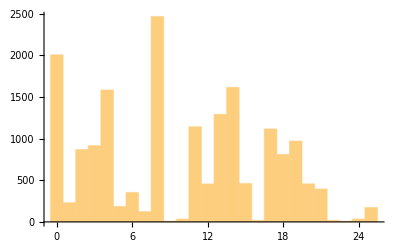

-Graphics-

```mathematica
blocksize=6
key=PermKeyGen[]
ctx=EncodingFunction[key,repubblica]
DecodingFunction[key,ctx]

Histogram[TextCode[ctx]]
Histogram[divina]
```

```mathematica
ctx
```

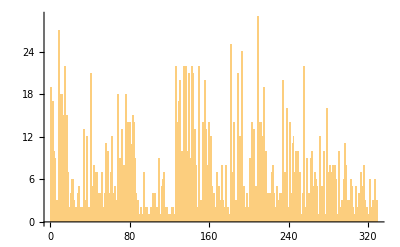

```mathematica
p=Partition[Take[TextCode[ctx],2000],2,1];
pairs=Union[p];
Histogram[p/.MapThread[Rule,{pairs,Range[Length[pairs]]}],Length[pairs]]
```

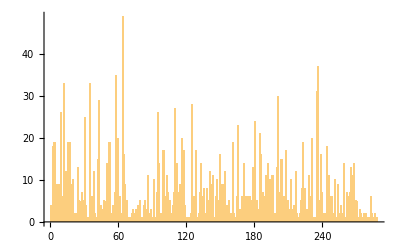

```mathematica
p=Partition[Take[divina,2000],2,1];
pairs=Union[p];
Histogram[p/.MapThread[Rule,{pairs,Range[Length[pairs]]}],Length[pairs]]
```

```mathematica
Partition[{1,23,4,5,6,78,9},3,3,1,0]
```

{{1,23,4},{5,6,78},{9,0,0}}

```mathematica
{a,b,c}[[{2,1,3}]]
```

{b,a,c}

{{{15,17},1},{{17,14},1},{{14,9},1},{{9,4},1},{{4,2},1},{{2,19},2},{{19,6},2},{{6,20},1},{{20,19},1},{{19,4},5},{{4,13},1},{{13,1},1},{{1,4},1},{{4,17},5},{{17,6},1},{{6,18},1},{{18,11},1},{{11,0},1},{{0,3},2},{{3,8},3},{{8,21},2},{{21,8},1},{{8,13},2},{{13,0},1},{{0,2},1},{{2,14},3},{{14,12},1},{{12,12},1},{{12,4},1},{{4,3},2},{{8,0},1},{{8,3},1},{{3,0},3},{{0,13},6},{{13,19},3},{{4,1},2},{{1,24},1},{{24,3},1},{{4,0},2},{{0,11},2},{{11,8},1},{{8,6},1},{{6,7},1},{{7,8},2},{{8,4},1},{{17,8},2},{{8,19},5},{{19,7},6},{{8,18},2},{{18,4},2},{{1,14},1},{{14,14},1},{{14,10},1},{{10,8},1},{{18,5},1},{{5,14},1},{{14,17},3},{{17,19},2},{{7,4},5},{{4,20},2},{{20,18},1},{{4,14},1},{{14,5},2},{{5,0},1},{{13,24},2},{{24,14},2},{{14,13},2},{{13,4},1},{{24,22},1},{{22,7},2},{{17,4},2},{{4,8},2},{{20,13},1},{{13,8},1},{{3,18},1},{{18,19},5},{{19,0},3},{{0,19},3},{{4,18},2},{{18,0},1},{{13,3},2},{{3,12},1},{{12,14},2},{{14,18},3},{{19,14},1},{{14,19},1},{{17,15},1},{{15,0},1},{{0,17},1},{{19,18},2},{{18,14},2},{{5,19},1},{{4,22},1},{{22,14},1},{{17,11},1},{{11,3},1},{{19,13},2},{{13,14},2},{{14,2},1},{{3,22},1},{{22,8},1},{{7,0},2},{{11,12},1},{{19,17},1},{{8,2},1},{{19,8},1},{{8,14},1},{{13,18},1},{{18,22},1},{{14,4},1},{{4,21},1},{{21,4},2},{{17,24},1},{{14,20},1},{{20,12},1},{{12,0},1},{{0,24},1},{{24,2},1},{{14,15},1},{{15,24},1},{{24,8},1},{{6,8},1}}

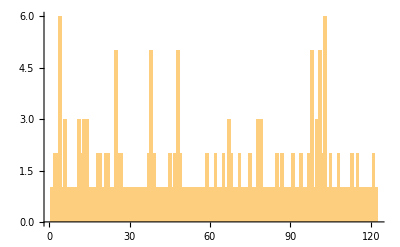

```mathematica
Tally[p=Partition[Take[divina,200],2,1]]
```

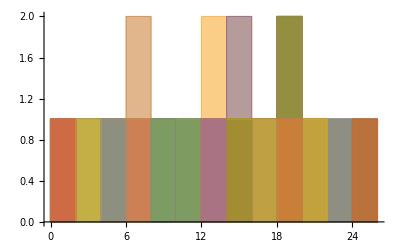

```mathematica
Histogram[p]
```